# Lecture 1 - Vicini

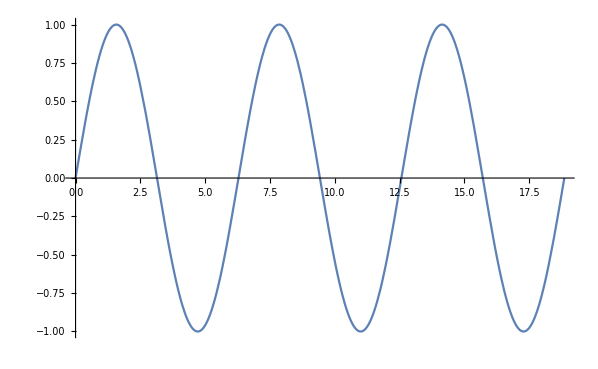

```mathematica
Plot[Sin[x],{x,0,6Pi}]
```

Le parentesi tonde servono solo per le espressioni algebriche. Gli argomenti di funzione sono circondate da parentesi quadre.

```mathematica
(a+b)(c+d)//Expand
```

a c+b c+a d+b d

Uno spazio fra simboli va inteso come un prodotto

Le graffe hanno vari ruoli. un esempio sono gli iteratori

```mathematica
{x,0,4}
```

```mathematica
Series[Sin[x],{x,0,7}]
```

x-x^3/6+x^5/120-x^7/5040+O[x]^8

```mathematica
Plot3D[Sin[x^2+y^2],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

In un ambiente di programmazione è utile sapere dov’è l’help

```mathematica
?? Plot3D
```

Per consultare tutti i comandi nativi che contengono una data stringa si usa: ?? *command *

```mathematica
?? *Plot*
```

Mathematica appartiene a pieno diritto alla categoria dei linguaggi di scrimpting. NOn è compilato come il c++, ma interpretato come Python. C’è quindi la possibilità di scrivere ed eseguire degli script. Basta un editor di testo in cui scirvere le struzioni.

In uno script, solo l’output dell’ultima riga viene stamapto (tranne nel caso in cui ci sia  ";")

```mathematica
D[f x^n,x]
```

f n x^(-1+n)

```mathematica
FullForm[f x^n]
```

Times[f,Power[x,n]]

```mathematica
D[f x^n,x]
```

f n x^(-1+n)

Con FullForm si vede nel dettaglio la struttura ad albero di una espressione di mathematica. é importante in mathematica riconoscere in una espressione la sua struttura. Bisogna distinguere fra head e argomenti.

```mathematica
FullForm[x+y+z]
FullForm[x y z]
```

Plus[x,y,z]

Times[x,y,z]

Si possono fare due cose completamente diverse semplicemente manipolando la head di una espressione. Vogliamo iniziare a lavorare sulla manipolazione delle espressioni, per creare delle funzioni. Creeremo un comando nostro che è analogo a quello di derivazione di mathematica.

Discussione sui tipi delle variabili. Non c’è bisogno di specificare il tipo, è simile a python. COmunque ci sono tutta una serie di tipi di variabili primitivi.

```mathematica
FullForm[a]
```

3

```mathematica
a=3
```

3

```mathematica
Head[4]
```

Integer

```mathematica
Head[x]
```

Symbol

```mathematica
Head[3.]
```

Real

```mathematica
Head["pippo"]
```

String

```mathematica
Head[1/7]
```

Rational

```mathematica
FullForm[1/7]
```

Rational[1,7]

N.B. Head non è che restituisce il tipo delle variabili, questa cosa sembra così solo negli oggetti elementari

```mathematica
Head[f[x,y]]
```

f

Guardiamo bene il seguente esempio. La sintassi [[ ]] serve per selezionare gli argomenti di una espressione, tenendoo conto che ci possono essere più argomenti innsettati

```mathematica
prova=f[(a+b)(c+d)]
```

f[(3+b) (c+d)]

```mathematica
prova[[1]]
```

(3+b) (c+d)

```mathematica
prova[[2]]
```

f[(3+b) (c+d)]⟦2⟧

```mathematica
prova[[1,2]]
```

c+d

```mathematica
prova[[1,1]]
```

3+b

```mathematica
prova[[1,2,1]]
```

c

```mathematica
prova[[0]]
```

f

```mathematica
prova[[1,0]]
```

Times

```mathematica
prova[[1,1,0]]
```

Plus

#### Prove a caso